## Problem 1 Scratch Work

```mathematica
z=Sum[1/n^2,{n,Infinity}]
pNot1=1-6/π^2//N
EbarSum=Sum[Log[n]/n^2,{n,Infinity}]//N
Ebar=(12k T EbarSum)/π^2
```

π^2/6

0.392073

0.937548

1.13992 k T

## Problem 3

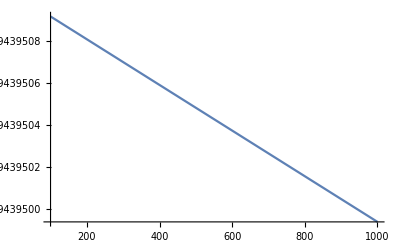

0.0807197

4.85386×10^-8

```mathematica
e=1.602*^-19;
u0=5*^6 e;
k=1.381*^-23;
r0=4*^-10;
B[T_]=-2π Integrate[r^2(ⅇ^((-(u0-u0/r0 r))/(k T))-1),{r,0,r0}];
Plot[B[T]/r0^3,{T,100,1000}]
B[200]6.022*^23 1000
B[200]6.022*^23 1000/(8.315 200 1000+1.34*^-28 6.022*^23 1000)
```

## Problem 6

```mathematica
μ0=.35;
α=.0015;
T0=240;
ef=μ0+α(T-T0);
k=8.617*^-5;
rhs=Integrate[(π^2 k^2 T)/(2 ef(μ0+α T-T0)),T];
Re[ⅇ^(rhs/.T->295-rhs/.T->0)] (* Imaginary numbers are small enough *)
```

1.21543

```mathematica
D[A Log[b u],u]
```

A/u

```mathematica
15*^3/45//N
```

333.333